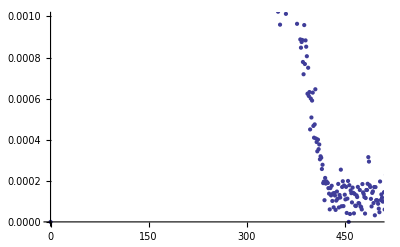

```mathematica
l="10";
v="9";
p="0.1";
d="0.085";
n=250;
ddcb=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam/DDCB-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ListPlot[ddcb,PlotRange->{{0,500},{0,0.001}}]
```

{(0.430279 ⅇ^(-0.0105196 r))/r^0.40315, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.430279 | 0.00449894 | 95.6401 | 3.55229×10^-165
ζ | 95.0603 | 1.83556 | 51.7881 | 1.53683×10^-115
b | -0.40315 | 0.00531967 | -75.7848 | 4.39527×10^-146}

{-0.807795-0.0097412 r-0.424373 Log[r], | Estimate | Standard Error | t-Statistic | P-Value
a | 0.44584 | 0.0151355 | 29.4567 | 1.56893×10^-73
ζ | 102.657 | 1.79757 | 57.1087 | 2.83352×10^-123
b | -0.424373 | 0.011179 | -37.9616 | 9.72763×10^-92}

Function[{r},(0.430279 ⅇ^(-0.0105196 r))/r^0.40315]

Function[{r},-0.807795-0.0097412 r-0.424373 Log[r]]

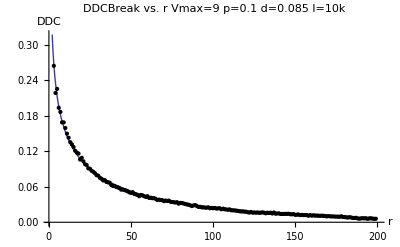

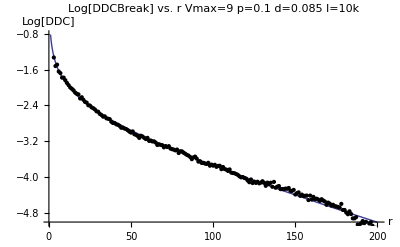

```mathematica
n=200;
l="10";
v="9";
p="0.1";
d="0.085";
ddcb=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/BreakJam/DDCB-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ClearAll[a,b];
ddcb1=ddcb[[All,1]];
ddcb2=ddcb[[All,2]];


data=Table[ddcb[[i]],{i,4,n}];
data2=Table[{ddcb1[[i]],Log[ddcb2[[i]]]},{i,4,n}];

model=a*Exp[-r/ζ]*r^b;
model2=Log[a]-r/ζ+b*Log[r];

nlf=NonlinearModelFit[data,model,{a,ζ,b},r];
nlf2=NonlinearModelFit[data2,model2,{a,ζ,b},r];

fit=FindFit[data,model,{a,ζ,b},r];
fit2=FindFit[data2,model2,{a,ζ,b},r];

val=nlf["ParameterTableEntries"];

nlf[{"BestFit","ParameterTable"}]
nlf2[{"BestFit","ParameterTable"}]

modelf1=Function[{r},Evaluate[model/.fit]]
modelf2=Function[{r},Evaluate[model2/.fit2]]

Plot[{modelf1[r]},{r,1,n},PlotLabel->"DDCBreak vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",Epilog->Map[Point,{data}],AxesLabel->{r,DDC},PlotRange->{Full,{0,1.2*ddcb2[[4]]}}]
Plot[{modelf2[r]},{r,1,n},PlotLabel->"Log[DDCBreak] vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",Epilog->Map[Point,{data2}],AxesLabel->{"r","Log[DDC]"},PlotRange->Full]
```

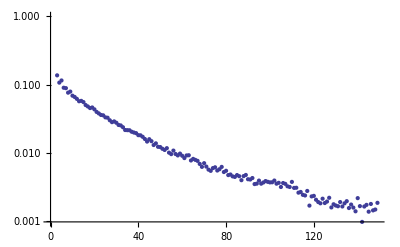

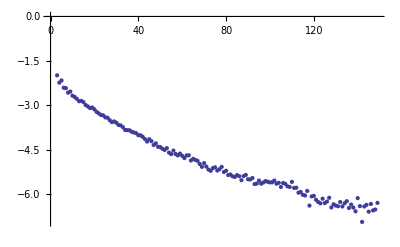

```mathematica
ListLogPlot[data]
ListPlot[data2]
```